# Упражнение 1. Въведение в Mathematica

## Някои приложения, които ще разгледаме в курса

### Едно приложение в компютърната графика

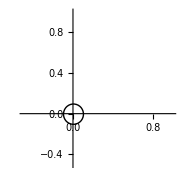
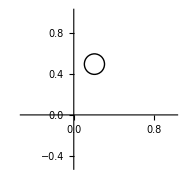
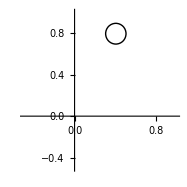

-Graphics- -Graphics- -Graphics-

```mathematica
poly[x_]=InterpolatingPolynomial[{{0,0},{0.2,0.5},{0.4,0.8}},x];
Animate[Graphics[Circle[{x,poly[x]},0.1],Axes->True,AxesOrigin->{0,0},PlotRange->{{-0.5,1},{-0.5,1}}],{x,0,0.4,0.01}]
```

### Моделиране нивото на въглероден диоксид в атмосферата

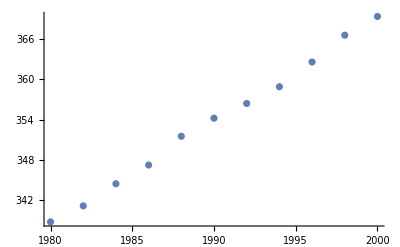

```mathematica
data = {{1980,338.7},{1982,341.1},{1984,344.4},{1986,347.2},{1988,351.5},{1990,354.2},{1992,356.4},{1994,358.9},{1996,362.6},{1998,366.6},{2000,369.4}};
plot1=ListPlot[data,PlotRange->All]
```

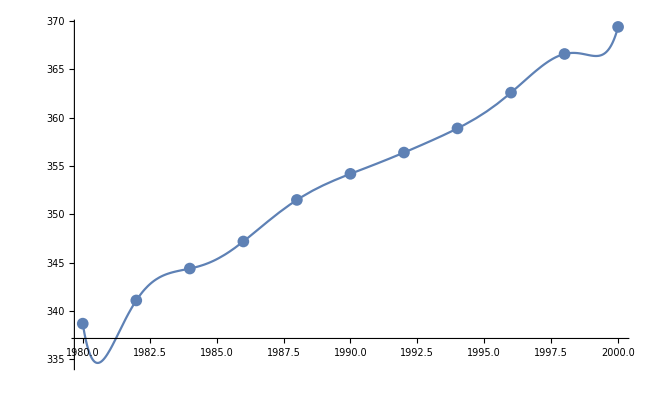

```mathematica
plot2=Plot[InterpolatingPolynomial[data,x],{x,1980,2000}];
Show[plot1,plot2 ,PlotRange->All]
```

## Основни операции

```mathematica
2+3
3.5-2.8
2*4
10/2
12^3
2x+3x
5!
Sqrt[121]
Sin[Pi]
ArcTan[1]
```

5

0.7

8

5

1728

5 x

120

11

0

π/4

## Скобите в Mathematica

### Кръгли скоби

```mathematica
x(x+2)^2
(x+y(1-y))^2
```

x (2+x)^2

(x+(1-y) y)^2

### Квадратни скоби - заграждат аргументите на даден оператор

```mathematica
Sqrt[60+4]
ArcSin[Sin[Pi/2]]
Log[E]
```

8

π/2

1

### Фигурни скоби - заграждат елементите на списък

```mathematica
{1,2,3,4}
```

{1,2,3,4}

### Mathematica не може да разбере какво имаме предвид със следните изрази:

```mathematica
[x+y(1-y)]^2  
(* (x+y(1-y))^2 *)
```

```mathematica
(1,2)
(* {1,2} *)
```

```mathematica
Sin(Pi)
(* Sin[Pi] *)
```

π Sin

## Символно и числено пресмятане

### Обикновено Mathematica смята символно (и следователно точно), ако не сме указали друго

```mathematica
123/Sqrt[768]
Cos[Pi/12]
Log[2]
```

(41 √3)/16

(1+√3)/(2 √2)

Log[2]

### Можем да смятаме числено по следния начин:

```mathematica
N[123/Sqrt[768]]
N[Cos[Pi/12]]
N[Log[2]]
```

4.43838

0.965926

0.693147

или

```mathematica
123./Sqrt[768]
Cos[Pi/12.]
Log[2.0]
```

4.43838

0.965926

0.693147

## Графики

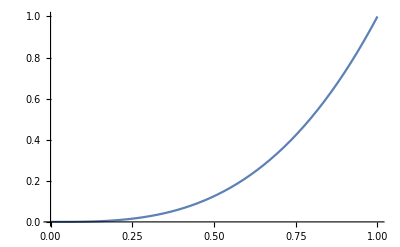

```mathematica
Plot[x^3, {x,0,1}]
```

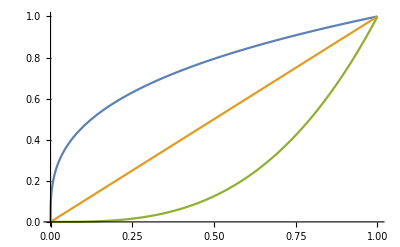

```mathematica
Plot[{x^(1/3),x,x^3}, {x,0,1}]
```

#### Задача 2: Постройте в една координатна система графиките на функцията f(x)=e^x и нейния полином на Тейлър от трета степен g(x) в интервала [-0.5, 0.5]. Постройте графиките на абсолютната и относителната грешка при приближаването на f(x) с g(x).

```mathematica
Series[E^x,{x,0,3}]
```

1+x+x^2/2+x^3/6+O[x]^4

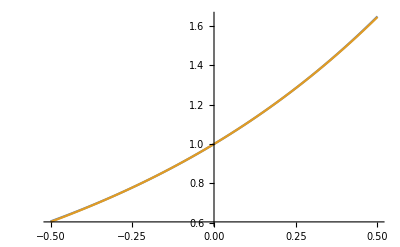

```mathematica
Plot[{E^x,1+x+0.5 x^2+0.1667 x^3},{x,-0.5,0.5}]
```

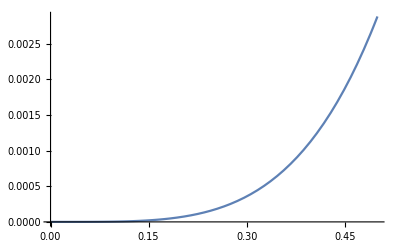

```mathematica
Plot[E^x-1-x-0.5 x^2-0.1667 x^3,{x,0,0.5},PlotRange->All]
```

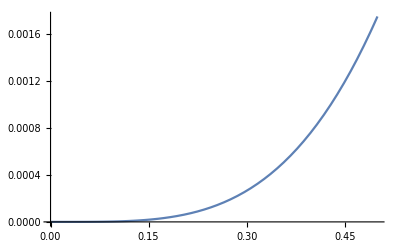

```mathematica
Plot[(E^x-1-x-0.5 x^2-0.16667 x^3)/E^x,{x,0,0.5},PlotRange->All]
```